```mathematica
(*  Guy F. Mongelli                               ChE 400
   Prof. Clark                                   9/14/2010     *)

(*Assignment #2
Problem 4     *)
```

```mathematica
Clear[a,b,fbas,f,fs,L,coeffs,fourier];
(*using a generic L until I can figure out how to introduce it as a variable*)
(*trying to figure out how to define functions as peicewise in mathematica*)
(*f[x_]:=x*(1+Abs[x])/;-1≤x<1;
f[x_]:=f[x+2]/;x≥1OR x<-1; 
f[1],f[3]  *)
```

```mathematica
L=1;
fbas[x_]:=x*(1+Abs[x])/;-L≤x<L
f[x_]:=fbas[Mod[x,2×L,-L]]
```

```mathematica
N[f[3]]
```

-2.

```mathematica
(*Defining the function as peicewise*)
```

```mathematica
(*g[x_]:=Piecewise[{{x*(1+Abs[x]),-1<=0<1},{f[x+2],x≥1}}];
g[3] *)
```

```mathematica
(*Defining the shifted function via Prof. Clark*)
```

```mathematica
(*defining the function to be approximated by the Fourier series*)
a[0]=N[Integrate[f[x],{x,-L,L}]]
```

1.66533×10^-16

```mathematica
a[n_]=(∫_-L^L x*(1+Abs[x])*Cos[(n*Pi*x)/L]ⅆx)/(2L)
```

0

```mathematica
b[n_]=FullSimplify[(∫_-L^L x*(1+Abs[x])*Sin[(n*Pi*x)/L]ⅆx)/L]
```

(-4+(4-4 n^2 π^2) Cos[n π]+6 n π Sin[n π])/(n^3 π^3)

```mathematica
coeffs=Table[{a[i],b[i]},{i,1,20}];
TableForm[coeffs]
```

0 | (-8+4 π^2)/π^3
0 | -2/π
0 | (-8+36 π^2)/(27 π^3)
0 | -1/π
0 | (-8+100 π^2)/(125 π^3)
0 | -2/(3 π)
0 | (-8+196 π^2)/(343 π^3)
0 | -1/(2 π)
0 | (-8+324 π^2)/(729 π^3)
0 | -2/(5 π)
0 | (-8+484 π^2)/(1331 π^3)
0 | -1/(3 π)
0 | (-8+676 π^2)/(2197 π^3)
0 | -2/(7 π)
0 | (-8+900 π^2)/(3375 π^3)
0 | -1/(4 π)
0 | (-8+1156 π^2)/(4913 π^3)
0 | -2/(9 π)
0 | (-8+1444 π^2)/(6859 π^3)
0 | -1/(5 π)

```mathematica
coeffs[[1]]
```

{0,(-8+4 π^2)/π^3}

```mathematica
coeffs[[2,1]]
```

0

```mathematica
fs[k_,x_]:=coeffs[[k,1]]*Cos[k*Pi*x/L]+coeffs[[k,2]]*Sin[k*Pi*x/L]
```

```mathematica
fourier[n_,x_]:=a[0]+∑_(k=1)^n fs[k,x]
```

```mathematica
fourier[5,x]
```

1.66533×10^-16+((-8+4 π^2) Sin[π x])/π^3-(2 Sin[2 π x])/π+((-8+36 π^2) Sin[3 π x])/(27 π^3)-Sin[4 π x]/π+((-8+100 π^2) Sin[5 π x])/(125 π^3)

```mathematica
fourier[10,x]
```

1.66533×10^-16+((-8+4 π^2) Sin[π x])/π^3-(2 Sin[2 π x])/π+((-8+36 π^2) Sin[3 π x])/(27 π^3)-Sin[4 π x]/π+((-8+100 π^2) Sin[5 π x])/(125 π^3)-(2 Sin[6 π x])/(3 π)+((-8+196 π^2) Sin[7 π x])/(343 π^3)-Sin[8 π x]/(2 π)+((-8+324 π^2) Sin[9 π x])/(729 π^3)-(2 Sin[10 π x])/(5 π)

```mathematica
Off[General::stop];
fourier[10,x]
```

1.66533×10^-16+((-8+4 π^2) Sin[π x])/π^3-(2 Sin[2 π x])/π+((-8+36 π^2) Sin[3 π x])/(27 π^3)-Sin[4 π x]/π+((-8+100 π^2) Sin[5 π x])/(125 π^3)-(2 Sin[6 π x])/(3 π)+((-8+196 π^2) Sin[7 π x])/(343 π^3)-Sin[8 π x]/(2 π)+((-8+324 π^2) Sin[9 π x])/(729 π^3)-(2 Sin[10 π x])/(5 π)

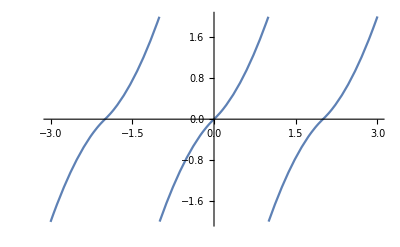

```mathematica
graphone=Plot[f[x],{x,-3,3},Exclusions->{-1,1}]
```

```mathematica
(*Manipulate[  consider manipulating k to find a reasonable value*)
```

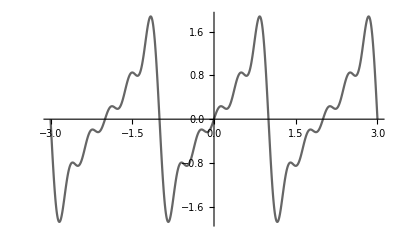

```mathematica
graphtwo=Plot[fourier[5,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

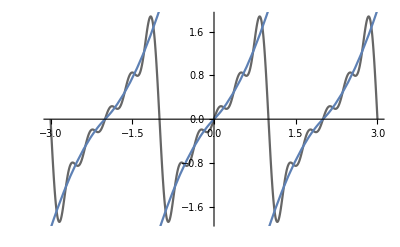

```mathematica
bothtwo=Show[graphtwo,graphone]
```

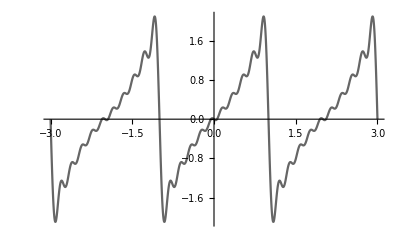

```mathematica
graphthree=Plot[fourier[10,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

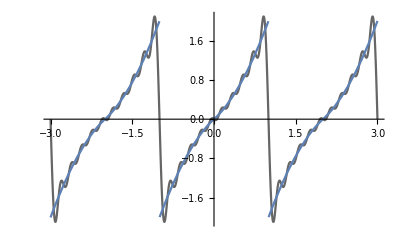

```mathematica
boththree=Show[graphthree,graphone]
```

```mathematica
graphsix=Plot[fourier[20,x],{x,-3,3},PlotStyle->GrayLevel[0.4]];
```

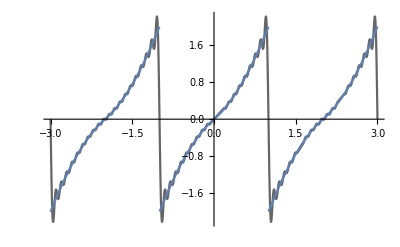

```mathematica
bothsix=Show[graphsix,graphone]
```

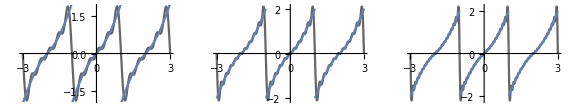

```mathematica
Show[GraphicsRow[{bothtwo,boththree,bothsix}]]
```

```mathematica
(*   The coefficients for the infinite series drop of as 1/n, therefore to acheive an estimated error of less than one percent, at least one hundred terms should be included in the approximation.   *)
```